## 2.13 Warnung : Das Peano Beispiel

-Graphics3D-

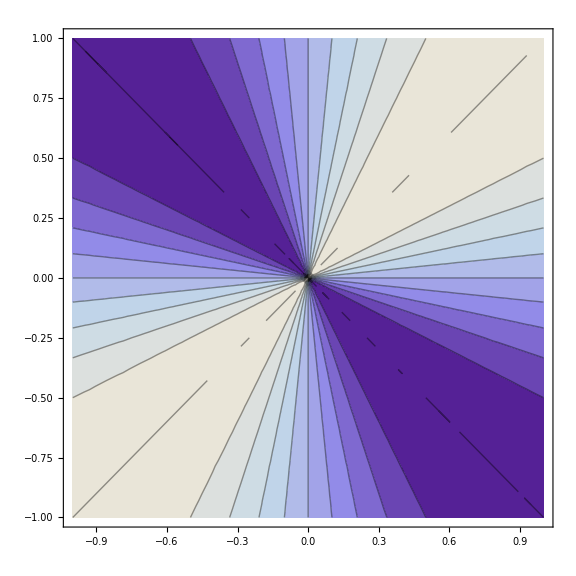

-Graphics3D-

```mathematica
f[x_,y_]:=x*y/(x^2+y^2) /;{x,y}≠{0,0}
f[x_,y_]:=0/;{x,y}={0,0}
Plot3D[f[x,y],{x,-1,1},{y,-1,1},ImageSize->Large]
ContourPlot[f[x,y],{x,-1,1},{y,-1,1},ImageSize->Large]
Plot3D[ {f[x,y],0},{x,-1,1},{y,-1,1},ImageSize->Large]
```